# Rapport projekt X

Mattias Sandberg, TIDB, matsandb@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Hitta lösningarna till polynomekvationen: 2 x^4+28/3 x^3-22/3 x^2-140/3 x+16=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Resultat

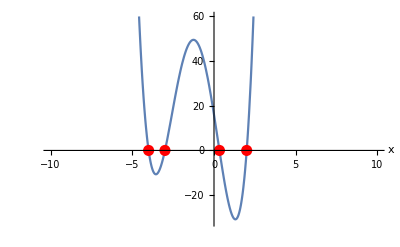
a) Rötterna är: {-4,-3,1/3,2}

b) Grafen är:  -Graphics-

## Kod

```mathematica
a) (*Kod till polynomekavationen:*) 
X= {x1,x2,x3,x4}=x/.Solve[2 x^4+(28/3)x^3-(22/3)x^2-140/3x+16==0]

b)(*kod till grafen för polynom ekvationen:*) ListPlot[X,AxesLabel->{"x","y"},AspectRatio->Automatic,PlotMarkers->{Automatic,Medium},Epilog->{EdgeForm[Red],FaceForm[]}]

Plot[2 x^4+(28/3)x^3-(22/3)x^2-140/3x+16, {x,-10,10}
PlotRange->{{-10,10},{-32,60}},Epilog->{Red,PointSize[0.02],Point[{x1,0}],Point[{x2,0}],Point[{x3,0}],Point[{x4,0}]},AxesLabel->Automatic]
```

Uppgift 2: Olikhet

## Sammanfattning

### Uppgift

Lös uppgift 21, 22 och 26  i kapitel 3 i boken Matematisk kommunikation, argumentation och skapande. Ge ett exakt svar. I de fall det är lämpligt illustrera lösningsområdet grafiskt.

### Resultat

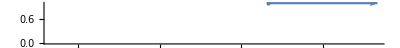
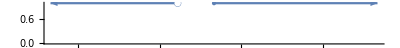
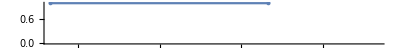
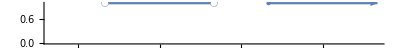
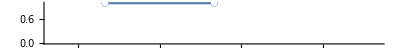
Uppgift 21: a) x≥2 -Graphics-,
 b) x<1/3||x≥1 -Graphics-,
 c)  -2≤x≤2 -Graphics-,

 d)  -1<x<1||x≥2 -Graphics-,
 e)  -1<x<1 -Graphics-, 
//Fick som tips av kamraträttning att visualisera uppgidt 21!
Upggift 22: a) False, b) 1/2≤x≤3 c) x==1, d) 0≤x≤4

Upggift 26: a) x==-1||x==4, b) x==0||x==1||x==1/2 (1-√17)||x==1/2 (1+√17)

## Kod

```mathematica
Uppgift 21:a) Reduce[(x-2)/(x^2+1)≥0, x, Reals]
NumberLinePlot[(x-2)/(x^2+1)≥0,{x,-2,4}]
```

```mathematica
Uppgift 21:b) Reduce[2/(3x-1)<=1, x, Reals]
NumberLinePlot[2/(3 x-1)≤1,{x,-2,4}]
```

```mathematica
Uppgift 21:c) Reduce[4/(x^2+4)≥(1/2), x, Reals]
NumberLinePlot[4/(x^2+4)≥(1/2),{x,-2,4}]
```

```mathematica
Uppgift 21:d) Reduce[(x-2)/(x^2-1)≥0, x, Reals]
NumberLinePlot[(x-2)/(x^2-1)≥0,{x,-2,4}]
```

```mathematica
Uppgidt 21:e) Reduce[((x-2)/(x-1))≥1+((2x)/(x+1)), x, Reals]
NumberLinePlot[((x-2)/(x-1))≥1+((2x)/(x+1)), {x, -2, 4}]
```

```mathematica
Uppgift 22:a)Reduce[√(x+1)<=-√(2+x),x,Reals]
```

```mathematica
Uppgidt 22:b) Reduce[Sqrt[2 x-1]>-1 (Sqrt[3-x]),x,Reals]
```

```mathematica
Uppgift 22:c) Reduce[√(x^2-1)<=-√(2 x^2-2x),x,Reals]
```

```mathematica
Uppgift 22:d) Reduce[(2+Sqrt[x]>=x),x,Reals]
```

```mathematica
Uppgift 26:a)Reduce[Abs[x-1]+Abs[x-2]==5,x,Reals]
```

```mathematica
Uppgift 26:b) Reduce[Abs[x^2-x-2]==2,x,Reals]
```

Uppgift 3: Bionomisk ekvation

## Sammanfattning

### Uppgift

Finn lösningen till ekvationen z^5=-3+3i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

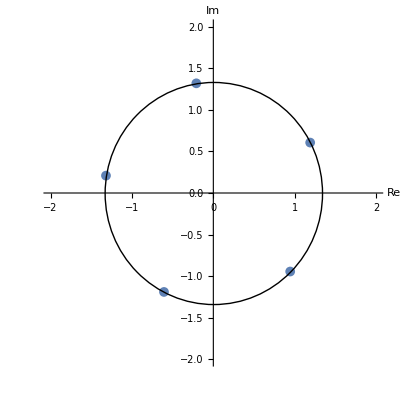
Svar: Lösningen till ekavtionen z^5=-3+3i är: 

{(-3+3 ⅈ)^(1/5),(-3+3 ⅈ)^(1/5) (-1)^(2/5),-(-3+3 ⅈ)^(1/5) (-1)^(3/5),(-3+3 ⅈ)^(1/5) (-1)^(4/5),-(-3)^(1/5) (-1+ⅈ)^(1/5)}

Grafisk visulation: -Graphics-

## Kod

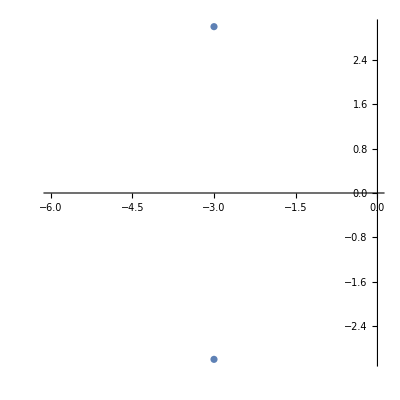
```mathematica
(*kod till Rötterna för ekvationen*)

z^5=-3+3I
Quit[]
z1 = -3+3I;
cz1 = -3-3I; 
Arg[z1]
Abs[z1]
(3 π)/4
3 √2

ComplexListPlot[{z1, cz1}]
-Graphics-

list= Solve[z^5+3-3I==0]
{{z->(-3+3 ⅈ)^(1/5)},{z->(-3+3 ⅈ)^(1/5) (-1)^(2/5)},{z->-(-3+3 ⅈ)^(1/5) (-1)^(3/5)},{z->(-3+3 ⅈ)^(1/5) (-1)^(4/5)},{z->-(-3)^(1/5) (-1+ⅈ)^(1/5)}}

Z = {z1, z2, z3, z4,z5} = z/.Solve[z^5+3-3I==0]
{(-3+3 ⅈ)^(1/5),(-3+3 ⅈ)^(1/5) (-1)^(2/5),-(-3+3 ⅈ)^(1/5) (-1)^(3/5),(-3+3 ⅈ)^(1/5) (-1)^(4/5),-(-3)^(1/5) (-1+ⅈ)^(1/5)}
```

```mathematica
(*Kod till uträkningen för den grafiska visualiseringen*)

pp=Table[{Re[Z[[i]]], Im[Z[[i]]]}, {i, 1, 5}]
{{Re[(-3+3 ⅈ)^(1/5)],Im[(-3+3 ⅈ)^(1/5)]},{Re[(-3+3 ⅈ)^(1/5) (-1)^(2/5)],Im[(-3+3 ⅈ)^(1/5) (-1)^(2/5)]},{Re[-(-3+3 ⅈ)^(1/5) (-1)^(3/5)],Im[-(-3+3 ⅈ)^(1/5) (-1)^(3/5)]},{Re[(-3+3 ⅈ)^(1/5) (-1)^(4/5)],Im[(-3+3 ⅈ)^(1/5) (-1)^(4/5)]},{Re[-(-3)^(1/5) (-1+ⅈ)^(1/5)],Im[-(-3)^(1/5) (-1+ⅈ)^(1/5)]}}

z1*z2*z3*z4*z5
-3+3 ⅈ
N[Re[(-3+3 ⅈ)^(1/5)]]
1.189619664737166

ListPlot[pp, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},PlotRange->{{-2,2},{-2,2}},Epilog->{Circle[{0,0},Abs[z1]]}]
-Graphics-
```

```mathematica
(*Jag fick hjälp av en anna grupp med den grafiska visuliseringen av lösningsmängden*)
```

Uppgift 4: Arean av en cirkel och närmevärde till Pi

## Sammanfattning

### Uppgift

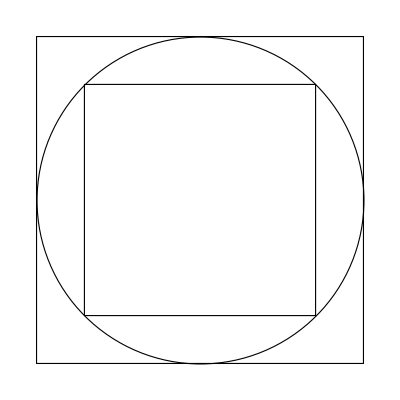
En kvadrat kan skrivas in i en cirkel och en cirkel kan skrivas in i en kvadrat, vilket ger figuren nedan. Antag att cirkeln har radien r=1.
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
-Graphics-
Från figuren kan vi konstatera att cirkelns area är mindre än 2^2=4 och större än (2/√2)^2=2. Det betyder att vi kan bestämma π=3±1. Dvs medelvärdet av 4+2 och det absoluta felet till närmevärdet. Då cirkelns area i detta fall är π r^2= π, så är detta också en metod att bestämma ett närmevärde till π. 
Vi kan också se arean för en kvadrat som fyrsidig polygon där arean kan bestämmas av fyra trianglar.
Använd ovanstående metod med reglebundna polygoner med fler sidor än fyra och beräkna ett mer exakt värde på π. Jämför sedan med värdet på Pi i Mathematica (se nedan med 10 siffor). Du får använda trigonometriska funktioner för att bestämma arean av trianglarna. 
Rita en graf för hur min och max värdet konvergerar mot Pi som en funktion av antal sidor på polygonen.
N[Pi, 10]
3.141592654

### Resultat

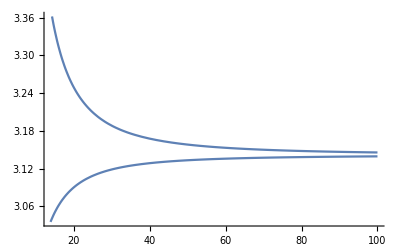
Svar: Graf över hur min och max värdet konvergerar mot Pi som en funktion av antal sidor på polygonen:

-Graphics-

## Kod

```mathematica
Quit[]
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
-Graphics-
(*a är antalet sidor i kvadraten*)
```

```mathematica
g1[a_]= a* (0.5*Tan[(2π/a)])
```

0.5 a Tan[(2 π)/a]

```mathematica
(*Polygonerna Pi för att beräkna vinklar i Polygonerna*)
```

```mathematica
g1[100]
```

3.14573

```mathematica
(*Beräkning av minsta möjliga Pi*)
```

```mathematica
p1 = Plot[g1[a], {a, 5, 100}]
```

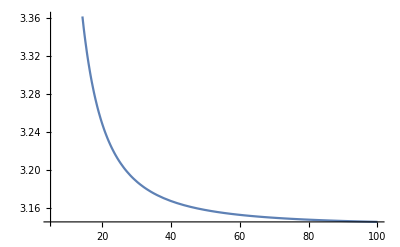

```mathematica
(*Arean av polygoner som ligger i cirkel, a antal sidor*)
```

```mathematica
g2[a_] = a*0.5*Sin[2π/a]
```

0.5 a Sin[(2 π)/a]

```mathematica
g2[100]
```

3.13953

```mathematica
(*Beräkning av maximala värdet för Pi*)
```

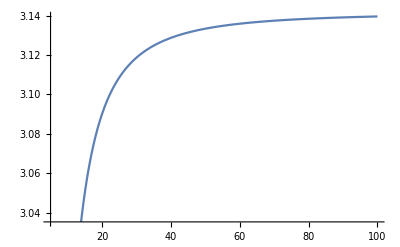

```mathematica
g2= Plot[g2[a], {a, 5, 100}]
```

```mathematica
(*båda graferna samsatta i samma kartesiska koordinatsystem*)
```

```mathematica
Show [p1, p2, PlotRange  -> All]
```

-Graphics-

```mathematica
N[Pi, 10]
```

3.141592654

```mathematica
(*Jag beräknar både minsta och störta värdet på Pi med trigonometriska funktioner. Sedan lade jag ihop graferna i ett kartesiska koordinatsystem och jämförde med det riktiga värdet på Pi (med 10st decimaler). Båda metoder närmar sig Pi när antalet polygoner i cirkeln och utanförcirkeln ökar*)

(*Jag fick hjälp av en annan grupp som hade fått hjälp av Fadil under en Datorlaborationsövning. framföralt med hur man skulle tolka frågan och vad det var man skulle beräkna och visulaisera grafiskt*)
```